```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.2, 0.3, 0.4, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-4 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.0001;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

```mathematica
(*N=3 - No Solution with equal Rabi. Possible with different Rabi, but areas are higher than BB4 below*)
```

BB4; p=1, 1/2, 1/4, error=0.0001

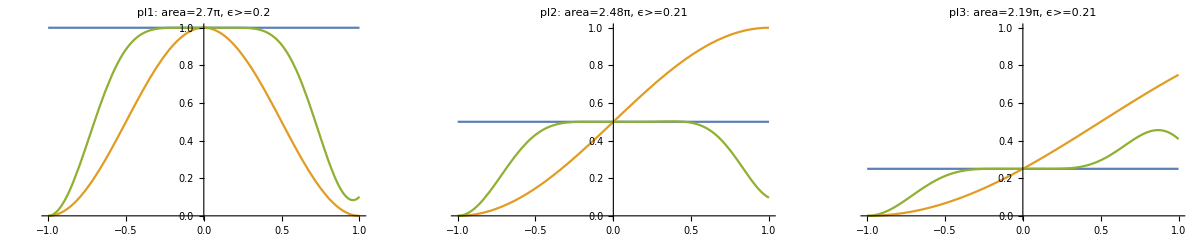

```mathematica
(*N=4 - BW=0.3 possible with different Rabi*)
(*Choose this*)
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,  totalArea[rule,4]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,4]]

pl1=pltS[1,{Δ1->-0.9267,Δ2->0.0227,Ω1->0.6750},"pl1"];
pl2=pltN[1/2,{Δ1->0.6465,Δ2->-0.0024,Δ3->-1.1049,Δ4->0.6265,Ω1->0.6197},"pl2"];
pl3=pltN[1/4,{Δ1->0.9445,Δ2->0.379,Δ3->-0.0641,Δ4->0.8702,Ω1->0.5467},"pl3"];

GGrid[Text[Style["BB4; p=1, 1/2, 1/4"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
```

```mathematica
(*N=5, 6, 7 DO NOT OFFER SMALLER PULSE AREAS THAN N=4 -- however larger bandwidhts can be obtained*)
```

BB5 p=1, 1/2, 1/4, error=0.0001

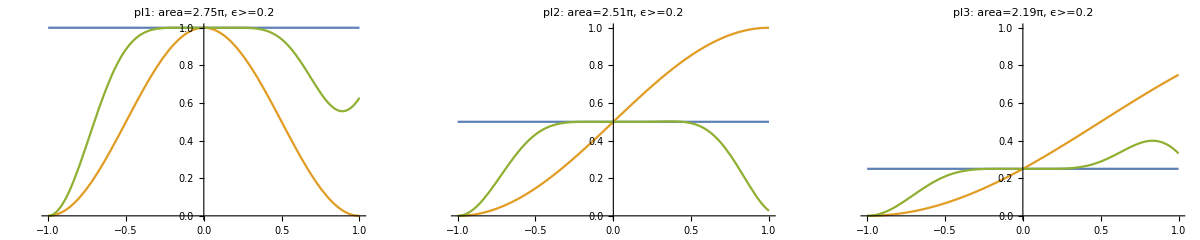

```mathematica
(*N=5 - NO USE, BB4 provides the same or smaller areas. BW=0.3 possible with different Rabi*)
sequence=U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[0,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,  totalArea[rule,5]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,5]]

pl1=pltS[1,{Δ1->0.8746,Δ2->0.1360,Ω1->0.5498},"pl1"];
pl2=pltN[1/2,{Δ1->0.7956,Δ2->0.4681,Δ3->-0.0785,Δ4->-0.0276,Δ5->0.8987,Ω1->0.5011},"pl2"];
pl3=pltN[1/4,{Δ1->0.0409,Δ2->0.7522,Δ3->0.2713,Δ4->-0.0885,Δ5->-0.9226,Ω1->0.438},"pl3"];

GGrid[Text[Style["BB5 p=1, 1/2, 1/4"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
```

BB6 p=1, 1/2, 1/4, error=0.0001

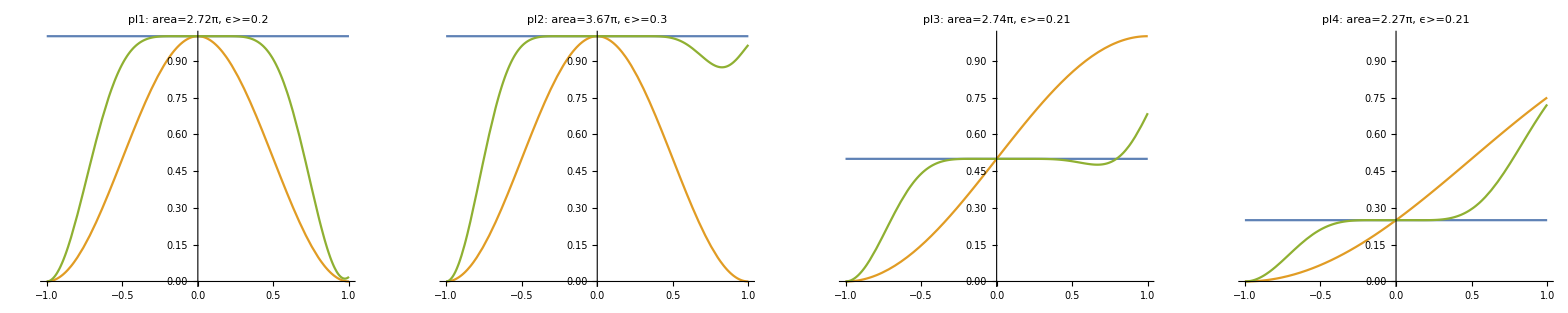

```mathematica
(*N=6 - NO USE, BB4 provides the same or smaller areas. BW=0.3 possible, however*)
sequence=U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,6]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,totalArea[rule,6]]

pl1=pltS[1,{Δ1->-0.1922,Δ2->0.3621,Δ3->0.6779,Ω1->0.4537},"pl1"];
pl2=pltS[1,{Δ1->0.5918,Δ2->0.5951,Δ3->-0.7717,Ω1->0.6118},"pl2"];

pl3=pltN[1/2,{Δ1->0.6843,Δ2->0.3391,Δ3->0.0205,Δ4->0.7819,Δ5->-0.7953,Δ6->-0.3044,Ω1->0.456},"pl3"];

pl4=pltN[1/4,{Δ1->0.1280,Δ2->0.6134,Δ3->0.1144,Δ4->0.7385,Δ5->-0.8724,Δ6->-0.0934,Ω1->0.3777},"pl4"];

GGrid[Text[Style["BB6 p=1, 1/2, 1/4"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
```

BB7 p=1, 1/2, 1/4, error=0.0001

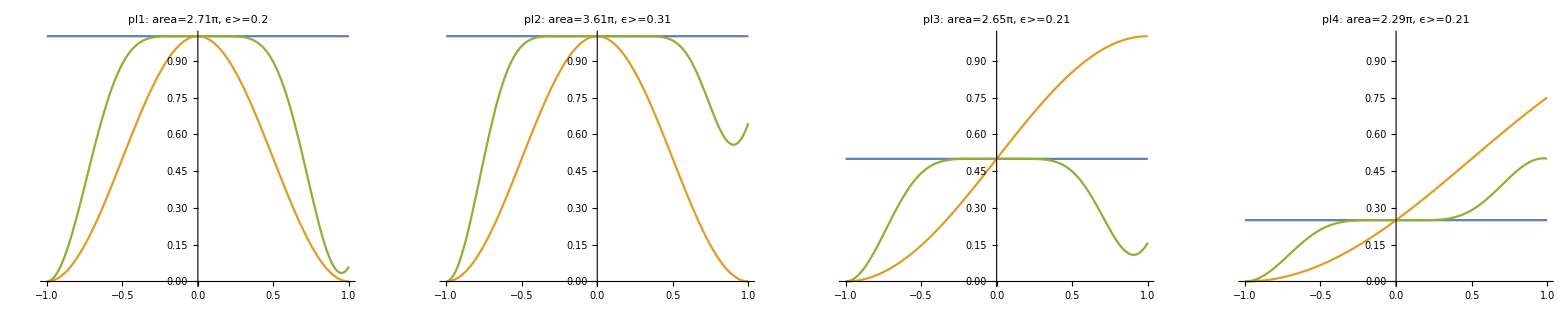

```mathematica
(*N=7 - NO USE, BB4 provides the same or smaller areas. BW=0.3 possible, however*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[0,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,7]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,7]]

pl1=pltS[1,{Δ1->-0.1770,Δ2->0.136,Δ3->0.6645,Ω1->0.3877},"pl1"];
pl2=pltS[1,{Δ1->0.9507,Δ2->0.1825,Δ3->0.1805,Ω1->0.5153},"pl2"];

pl3=pltN[1/2,{Δ1->0.08121,Δ2->0.53654,Δ3->-0.115,Δ4->-0.31977,Δ5->-0.7422,Δ6->0.12535,Δ7->0.58214,Ω1->0.37925},"pl3"];

pl4=pltN[1/4,{Δ1->-0.12461,Δ2->-0.80658,Δ3->0.53792,Δ4->-0.34542,Δ5->-0.09045,Δ6->-0.50421,Δ7->-0.58676,Ω1->0.32688},"pl4"];

GGrid[Text[Style["BB7 p=1, 1/2, 1/4"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
```